```mathematica
Remove["Global`*"];
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
ϵ0 = QuantityMagnitude[UnitConvert[Quantity["VacuumPermittivity"]]];
μ0 = QuantityMagnitude[UnitConvert[Quantity["VacuumPermeability"]]];
qe = QuantityMagnitude[UnitConvert[Quantity["ElementaryCharge"]]];
c   = QuantityMagnitude[UnitConvert[Quantity["SpeedOfLight"]]];
me = QuantityMagnitude[UnitConvert[Quantity["ElectronMass"]]];
amu= QuantityMagnitude[UnitConvert[Quantity["AtomicMassUnit"]]];
kb  =QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]]];
```

## Calculating the Potential and E-field for the Clam-Shells

Calculate the potential for the clam-shells with the top shell at 500 V and the bottom grounded

```mathematica
xend = 0.95 (* the x-value where the electrode ends *);
```

```mathematica
sc=NDSolveValue[{Laplacian[V[x,y],{x,y}]==0, DirichletCondition[V[x,y]==500.0,x^2+y^2== 1 && -xend≤x≤xend && y>0.0 ],DirichletCondition[V[x,y]==0.0,x^2+y^2== 1 && -xend≤x≤xend && y<0.0 ]},V,{x,y}∈ Disk[]];
```

Calculate the angle where the clam-shell ends

```mathematica
Angle = ArcTan[xend,Sqrt[1.0-xend^2]];
```

Plot the potential

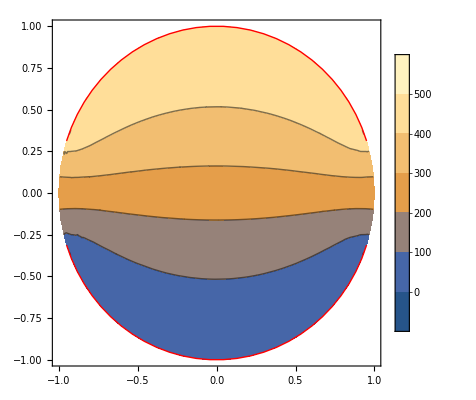

```mathematica
ContourPlot[sc[x,y],{x,y}∈ Disk[], PlotLegends->BarLegend[Automatic,LabelStyle->{FontWeight->"Bold",FontSize->12}], BaseStyle->{FontWeight->"Bold",FontSize->12},Epilog->{Directive[{Thick,Red}],Circle[{0,0},1,{Angle,Pi-Angle}],Circle[{0,0},1,{-Angle,-Pi+Angle}]}]
```

Plot the Electric Field

```mathematica
Eclam[x_,y_] = -Grad[sc[x,y],{x,y}];
```

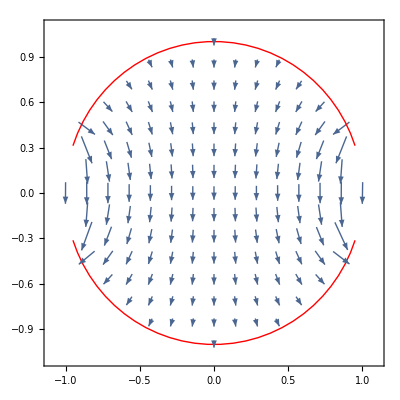

```mathematica
VectorPlot[Eclam[x,y],{x,y}∈ Disk[], BaseStyle->{FontWeight->"Bold",FontSize->12},Epilog->{Directive[{Thick,Red}],Circle[{0,0},1,{Angle,Pi-Angle}],Circle[{0,0},1,{-Angle,-Pi+Angle}]}]
```

## Calculating the Potential and E-field for Parallel Plates

Calculate the potential for the clam-shells with the top shell at 500 V and the bottom grounded

```mathematica
scp=NDSolveValue[{Laplacian[V[x,y],{x,y}]==0, DirichletCondition[V[x,y]==500.0,y== 1  ],DirichletCondition[V[x,y]==0.0,y== -1  ]},V,{x,-1,1},{y,-1,1}];
```

Plot the potential

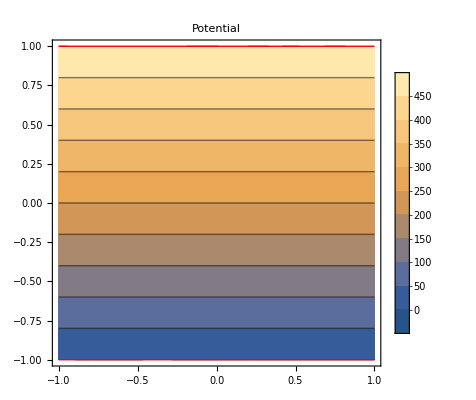

```mathematica
ContourPlot[scp[x,y],{x,-1,1},{y,-1,1}, PlotLegends->Automatic, PlotLabel->"Potential",Epilog->{Directive[{Thick,Red}],Line[{{-1,1},{1,1}}],Line[{{-1,-1},{1,-1}}]}]
```

Plot the Electric Field

```mathematica
Epp[x_,y_] = -Grad[scp[x,y],{x,y}];
```

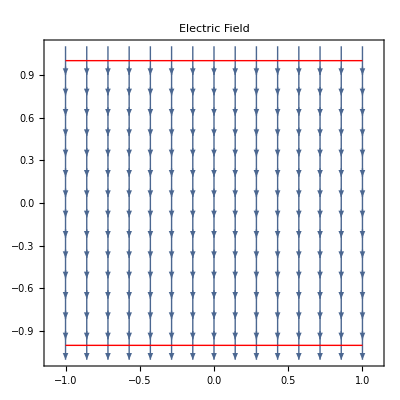

```mathematica
VectorPlot[Epp[x,y],{x,-1,1},{y,-1,1}, PlotLabel->"Electric Field",Epilog->{Directive[{Thick,Red}],Line[{{-1,1},{1,1}}],Line[{{-1,-1},{1,-1}}]}]
```

Calculate the ratio of the electric fields at the center of the cavity:

E_clam/E_parallel

```mathematica
Norm[Eclam[0,0]]
```

310.446

```mathematica
Norm[Epp[0,0]]
```

250.

```mathematica
Norm[Eclam[0,0]]/Norm[Epp[0,0]]
```

1.24178